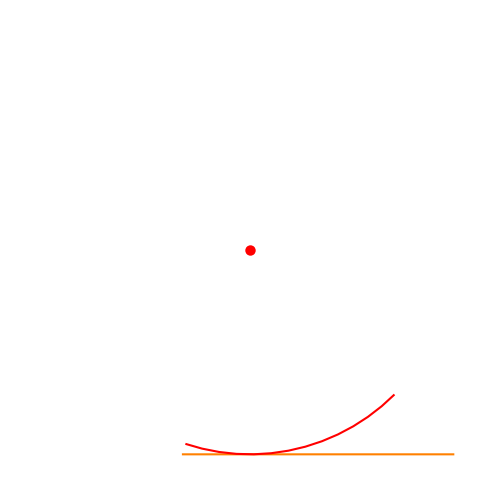

```mathematica
A = {0,0};
B = {1,0};
P = {.25,.75};
θ = ArcCos[((B-P).({P⟦2⟧,0}))/(Norm[(B-P)]Norm[({P⟦2⟧,0})])];
dθ = ArcCos[((A-P).(B-P))/(Norm[(A-P)]Norm[(B-P)])];

Graphics[{
Dashed,White,Thickness[.003],Circle[P,P⟦2⟧],
Thickness[.002],Line[{P,A}],Line[{P,B}],
Dashing->None,Orange, Thickness[.003],Line[{A,B}],
Red,PointSize[0.015],Point[P],
Circle[P,P⟦2⟧,{-θ,-θ-dθ}]
},ImageSize->500]
```

```mathematica
ClickPane[Framed@Dynamic[
Plot[eqn,{x,-10,10},Epilog->Style[Point[data],Red,PointSize[0.02]],ImageSize->{500,500},PlotRange->{-10,10},AspectRatio->1]],(If[Length[data]<c,AppendTo[data,#],data={#}])&],
```